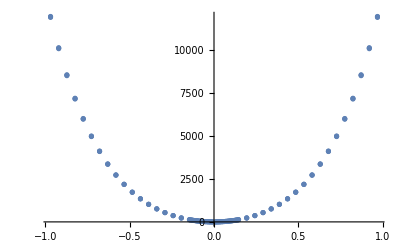

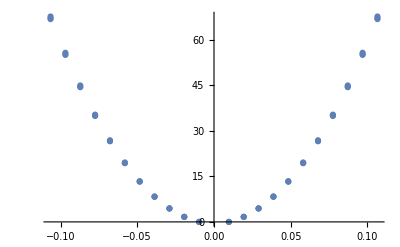

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC"];
filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_3200K_energy_displacement_harmonic"};
CarbonPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
CarbonPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot@CarbonPotentialEinstein
Show@ListPlot@CarbonPotentialEinsteinHarmonic
```

5875.09 x^2

11.006-1.75275×10^-13 x+5379.79 x^2+7746.25 x^4

-0.594182+1.11197×10^-12 x+5890.1 x^2+6025.53 x^4+1337.75 x^6

-0.16809-5.0351×10^-13 x+5858.52 x^2+6221.6 x^4+975.482 x^6+203.15 x^8

-0.622833-3.41389×10^-12 x+5906.28 x^2+5752.54 x^4+2486.22 x^6-1732.02 x^8+854.802 x^10

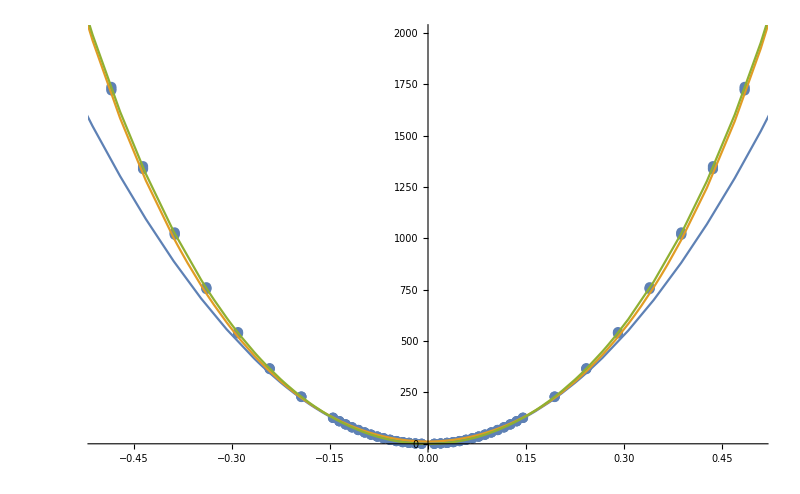

```mathematica
(*secondOrderFit=Fit[CarbonPotentialEinstein,{1,x,x^2},x]*)
secondOrderFit=Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]
fourthOrderFit=Fit[CarbonPotentialEinstein,{1,x,x^2,x^4},x]
sixthOrderFit=Fit[CarbonPotentialEinstein,{1,x,x^2,x^4,x^6},x]
eigthOrderFit=Fit[CarbonPotentialEinstein,{1,x,x^2,x^4,x^6,x^8},x]
tenthOrderFit=Fit[CarbonPotentialEinstein,{1,x,x^2,x^4,x^6,x^8,x^10},x]
nOrderFit={secondOrderFit,fourthOrderFit,sixthOrderFit,eigthOrderFit};
Show[{ListPlot[CarbonPotentialEinstein,ImageSize->800, PlotRange->{{-0.5,0.5},{0,2000
}}],Plot[{secondOrderFit,fourthOrderFit,sixthOrderFit},{x,-1,1},ImageSize->1200]}]
```

```mathematica
CarbonPotentialEinstein//MatrixForm
```

(-0.9685 | 11900.4
-0.9685 | 11939.9
-0.9685 | 11957.4
-0.92007 | 10080.3
-0.92007 | 10116
-0.92007 | 10138.1
-0.87165 | 8509.43
-0.87165 | 8539.64
-0.87165 | 8562.79
-0.82322 | 7151.34
-0.82322 | 7175.93
-0.82322 | 7198.01
-0.7748 | 5977.81
-0.7748 | 5997.62
-0.7748 | 6017.79
-0.72637 | 4965.82
-0.72637 | 4982.09
-0.72637 | 5000.23
-0.67795 | 4095.87
-0.67795 | 4109.68
-0.67795 | 4125.89
-0.62952 | 3350.87
-0.62952 | 3362.85
-0.62952 | 3377.26
-0.5811 | 2715.48
-0.5811 | 2725.94
-0.5811 | 2738.65
-0.53267 | 2175.98
-0.53267 | 2185.02
-0.53267 | 2196.08
-0.48425 | 1720.11
-0.48425 | 1727.77
-0.48425 | 1737.23
-0.43582 | 1337.08
-0.43582 | 1343.4
-0.43582 | 1351.31
-0.3874 | 1017.47
-0.3874 | 1022.5
-0.3874 | 1028.93
-0.33897 | 753.12
-0.33897 | 756.97
-0.33897 | 762.01
-0.29055 | 537.09
-0.29055 | 539.89
-0.29055 | 543.68
-0.24212 | 363.53
-0.24212 | 365.45
-0.24212 | 368.12
-0.1937 | 227.69
-0.1937 | 228.88
-0.1937 | 230.62
-0.14527 | 125.78
-0.14527 | 126.43
-0.14527 | 127.42
-0.13559 | 109.2
-0.13559 | 109.77
-0.13559 | 110.63
-0.1259 | 93.84
-0.1259 | 94.33
-0.1259 | 95.08
-0.11622 | 79.69
-0.11622 | 80.11
-0.11622 | 80.74
-0.10653 | 66.73
-0.10653 | 67.08
-0.10653 | 67.61
-0.09685 | 54.95
-0.09685 | 55.23
-0.09685 | 55.67
-0.08716 | 44.32
-0.08716 | 44.55
-0.08716 | 44.91
-0.07748 | 34.85
-0.07748 | 35.03
-0.07748 | 35.31
-0.06779 | 26.52
-0.06779 | 26.65
-0.06779 | 26.87
-0.05811 | 19.31
-0.05811 | 19.41
-0.05811 | 19.57
-0.04842 | 13.23
-0.04842 | 13.3
-0.04842 | 13.4
-0.03874 | 8.26
-0.03874 | 8.3
-0.03874 | 8.37
-0.02905 | 4.4
-0.02905 | 4.42
-0.02905 | 4.46
-0.01937 | 1.65
-0.01937 | 1.66
-0.01937 | 1.67
-0.00968 | 0
-0.00968 | 0
-0.00968 | 0
0.00968 | 0
0.00968 | 0
0.00968 | 0
0.01937 | 1.65
0.01937 | 1.66
0.01937 | 1.67
0.02905 | 4.4
0.02905 | 4.42
0.02905 | 4.46
0.03874 | 8.26
0.03874 | 8.3
0.03874 | 8.37
0.04842 | 13.23
0.04842 | 13.3
0.04842 | 13.4
0.05811 | 19.31
0.05811 | 19.41
0.05811 | 19.57
0.06779 | 26.52
0.06779 | 26.65
0.06779 | 26.87
0.07748 | 34.85
0.07748 | 35.03
0.07748 | 35.31
0.08716 | 44.32
0.08716 | 44.55
0.08716 | 44.91
0.09685 | 54.95
0.09685 | 55.23
0.09685 | 55.67
0.10653 | 66.73
0.10653 | 67.08
0.10653 | 67.61
0.11622 | 79.69
0.11622 | 80.11
0.11622 | 80.74
0.1259 | 93.84
0.1259 | 94.33
0.1259 | 95.08
0.13559 | 109.2
0.13559 | 109.77
0.13559 | 110.63
0.14527 | 125.78
0.14527 | 126.43
0.14527 | 127.42
0.1937 | 227.69
0.1937 | 228.88
0.1937 | 230.62
0.24212 | 363.53
0.24212 | 365.45
0.24212 | 368.12
0.29055 | 537.09
0.29055 | 539.89
0.29055 | 543.68
0.33897 | 753.12
0.33897 | 756.97
0.33897 | 762.01
0.3874 | 1017.47
0.3874 | 1022.5
0.3874 | 1028.93
0.43582 | 1337.08
0.43582 | 1343.4
0.43582 | 1351.31
0.48425 | 1720.11
0.48425 | 1727.77
0.48425 | 1737.23
0.53267 | 2175.98
0.53267 | 2185.02
0.53267 | 2196.08
0.5811 | 2715.48
0.5811 | 2725.94
0.5811 | 2738.65
0.62952 | 3350.87
0.62952 | 3362.85
0.62952 | 3377.26
0.67795 | 4095.87
0.67795 | 4109.68
0.67795 | 4125.89
0.72637 | 4965.82
0.72637 | 4982.09
0.72637 | 5000.23
0.7748 | 5977.81
0.7748 | 5997.62
0.7748 | 6017.79
0.82322 | 7151.34
0.82322 | 7175.93
0.82322 | 7198.01
0.87165 | 8509.43
0.87165 | 8539.64
0.87165 | 8562.79
0.92007 | 10080.3
0.92007 | 10116
0.92007 | 10138.1
0.9685 | 11900.4
0.9685 | 11939.9
0.9685 | 11957.4)

```mathematica
(*Harmonic oscillator Schrodinger solution - http://mathematica.stackexchange.com/questions/32293/find-eigen-energies-of-time-independent-schr%C3%B6dinger-equation *)
```

```mathematica
xOp[dim_]:=SparseArray[{Band[{1,2}]->#,Band[{2,1}]->#},{#,#}&@dim]&[Table[Sqrt[i],{i,dim-1}]/Sqrt[2]]
xOp[8]//MatrixForm

eKin[dim_]:=1/2 SparseArray[{Band[{1,1}]->Table[i-1/2,{i,dim}],Band[{1,3}]->#,Band[{3,1}]->#},{#,#}&@dim]&[Table[-Sqrt[i (i+1)/2],{i,dim-2}]/Sqrt[2]]
eKin[8]//MatrixForm
```

(0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
1/(√2) | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | √(3/2) | 0 | 0 | 0 | 0
0 | 0 | √(3/2) | 0 | √2 | 0 | 0 | 0
0 | 0 | 0 | √2 | 0 | √(5/2) | 0 | 0
0 | 0 | 0 | 0 | √(5/2) | 0 | √3 | 0
0 | 0 | 0 | 0 | 0 | √3 | 0 | √(7/2)
0 | 0 | 0 | 0 | 0 | 0 | √(7/2) | 0)

(1/4 | 0 | -1/(2 √2) | 0 | 0 | 0 | 0 | 0
0 | 3/4 | 0 | -(√(3/2))/2 | 0 | 0 | 0 | 0
-1/(2 √2) | 0 | 5/4 | 0 | -(√3)/2 | 0 | 0 | 0
0 | -(√(3/2))/2 | 0 | 7/4 | 0 | -(√5)/2 | 0 | 0
0 | 0 | -(√3)/2 | 0 | 9/4 | 0 | -(√(15/2))/2 | 0
0 | 0 | 0 | -(√5)/2 | 0 | 11/4 | 0 | -(√(21/2))/2
0 | 0 | 0 | 0 | -(√(15/2))/2 | 0 | 13/4 | 0
0 | 0 | 0 | 0 | 0 | -(√(21/2))/2 | 0 | 15/4)

```mathematica
spectrum[n_,tolerance_: .01][potential_,var_]/;PolynomialQ[potential,var]:=Module[{x,h,e,v,c=CoefficientList[potential,var],min=First@Check[Minimize[potential,var],Print["No absolute potential minimum found. Make sure the leading power has a positive coefficient!"];
Abort[],Minimize::natt]},FixedPoint[{#[[1]]+1,Eigenvalues[h=eKin[#[[1]]]+N[Sum[c[[i]] MatrixPower[xOp[#[[1]]],i-1],{i,2,Length[c]}]+(c[[1]]-min) IdentityMatrix[#[[1]]]],-n]}&,{n+1,2 Reverse@Range[n]-1},SameTest->(Max@Abs[#1[[2]]-#2[[2]]]<tolerance&)];
{e,v}=Reverse/@Eigensystem[h,-n];
{e+min,ψe/@v}]
```

```mathematica
Format[ψe[l_List]]:=ψe[Row[{"«",Length[l],"»"}]]
ψe[l_List][x_]:=1/(Pi^(1/4))Exp[-x^2/2] l.(1/Sqrt[2^# #!] HermiteH[#,x]&[Range[Length[l]]-1])

plotSpectrum[data_,potential_,{var_,min_,max_}]:=Show[Apply[Plot[Evaluate[#1+(Last[#1]-First[#1])/(2+Length[#1])/2 Through[#2[var]]],{var,min,max},Prolog->{Gray,Map[Line[{{min,#},{max,#}}]&,#1]},Frame->True]&,data],Plot[potential,{var,min,max}]]
```

```mathematica
spectrum[2][1/2 x^2+x^8,x]
```

{{0.820282,3.00299},{ψe[«25»],ψe[«25»]}}

```mathematica
(*Mexican hat anharmonic oscillator Schrodinger solution - http://mathematica.stackexchange.com/questions/32293/find-eigen-energies-of-time-independent-schr%C3%B6dinger-equation *)
```

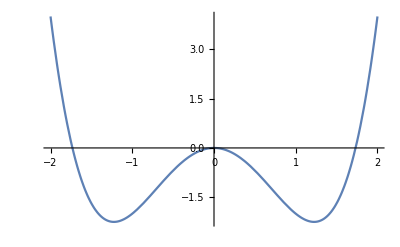

```mathematica
Plot[-3 x^2+x^4,{x,-2,2}]
```

```mathematica
ψ1=spectrum[5][-10 x^2+x^4,x]//Last//Last
```

ψe[«46»]

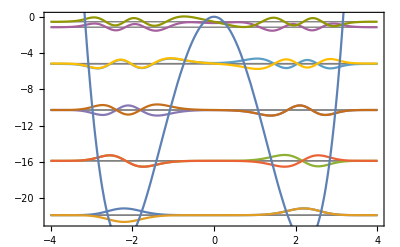

```mathematica
With[{v=-10 x^2+x^4,n=10},plotSpectrum[spectrum[n][v,x],v,{x,-4,4}]]
```

```mathematica
0.001*eigthOrderFit
```

0.001 (-0.16809-5.0351×10^-13 x+5858.52 x^2+1.16617×10^-11 x^3+6221.6 x^4-1.69952×10^-11 x^5+975.482 x^6+2.07898×10^-11 x^7+203.15 x^8)

```mathematica
spectrum[10][0.001*eigthOrderFit,x]
```

{{2.01939,6.52689,11.8533,17.8284,24.3677,31.4164,38.935,46.8936,55.2705,64.0362},{ψe[«100»],ψe[«100»],ψe[«100»],ψe[«100»],ψe[«100»],ψe[«100»],ψe[«100»],ψe[«100»],ψe[«100»],ψe[«100»]}}

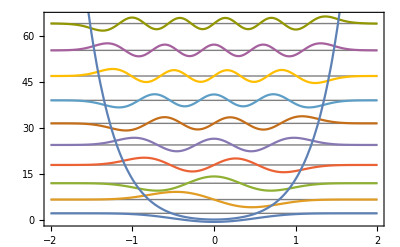

```mathematica
With[{v=0.001*eigthOrderFit,n=10},plotSpectrum[spectrum[n][v,x],v,{x,-2,2}]]
```